# Create Data

## Program

### load

```mathematica
Get["/Users/amanokou/SCRIPT-MATHEMATICA/SCRIPTS/polar.txt"]
```

### R <-> MMA

```mathematica
makeClusterFromRdata[rdata_]:=Map[Drop[#,-1]&,Gather[Map[Drop[#,1]&,Drop[rdata,1]],#1[[-1]]==#2[[-1]]&],{2}]
```

```mathematica
makeClusterFromRdata[rdata_,"Nohead"]:=Map[Drop[#,-1]&,Gather[Map[Drop[#,1]&,rdata],#1[[-1]]==#2[[-1]]&],{2}]
```

```mathematica
makeClusterFromRdata[rdata_,"NoID"]:=Map[Drop[#,-1]&,Gather[Drop[rdata,1],#1[[-1]]==#2[[-1]]&],{2}]
```

```mathematica
makeClusterFromRdata[rdata_,op__]:=If[
Length[Flatten[Union[{{op},{"NoID","Nohead"}}]]]==2,
Map[Drop[#,-1]&,Gather[rdata,#1[[-1]]==#2[[-1]]&],{2}]
]
```

```mathematica
(*makeClusterFromRdata[rdata_,"NoID","Nohead"]:=Map[Drop[#,-1]&,Gather[rdata,#1[[-1]]==#2[[-1]]&],{2}]*)
```

```mathematica
makeRClusterFromMMAClData[cl_List]:=Module[
{len,dim,ClIDs},
len=Length[cl];
dim=Length[cl[[1,1]]];
ClIDs=Table[i,{i,len}];
Flatten[Table[Map[Append[#,i]&,cl[[i]]],{i,len}],1]
]
```

```mathematica
createClusterdFileR[li_]:=Flatten[Table[Map[Append[#,n]&,li[[n]]],{n,Length[li]}],1]
```

## Prepare

```mathematica
SetDirectory["/Users/amanokou/gitsrc/ClusteringAdequation/data"]
```

/Users/amanokou/gitsrc/ClusteringAdequation/data

## Polar

```mathematica
rdata=Table[{RandomReal[{1,1.5}],RandomReal[{-1.1Pi,1.1Pi}]},{50}];
```

```mathematica
rdata
```

{{1.15172,3.34214},{1.38171,1.44508},{1.41134,3.19337},{1.34754,-0.483397},{1.02398,0.0669565},{1.34704,2.6248},{1.02265,0.963176},{1.02813,-2.50725},{1.29852,1.82979},{1.12575,2.5233},{1.09889,1.40853},{1.48006,2.80905},{1.21029,-0.822647},{1.38393,0.635037},{1.015,-0.66366},{1.43105,-1.5327},{1.15785,0.667804},{1.3477,-0.645483},{1.2161,0.172921},{1.18736,-0.492909},{1.43502,-3.44624},{1.31325,-1.24304},{1.02597,-1.73498},{1.43905,2.22598},{1.24908,1.01525},{1.41755,1.48882},{1.04758,3.22396},{1.06928,2.97691},{1.22965,0.497223},{1.21914,2.6322},{1.25326,0.0291051},{1.49211,-2.345},{1.32909,0.715473},{1.39212,2.31075},{1.23618,1.40765},{1.41132,-0.249424},{1.45146,-1.84889},{1.31535,-2.41485},{1.18613,3.27583},{1.2457,-1.15696},{1.13545,1.44093},{1.43262,2.37513},{1.28951,0.0621554},{1.07298,2.77026},{1.04554,1.89189},{1.33951,0.626863},{1.49646,2.32219},{1.45386,1.69838},{1.18704,-1.56366},{1.35301,3.24357}}

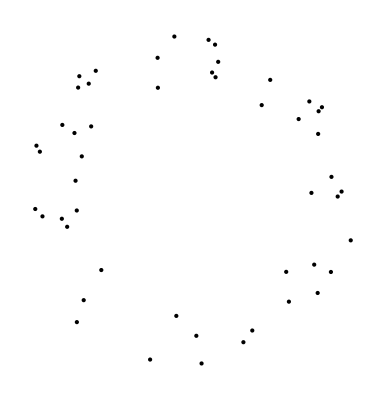

```mathematica
Graphics[Map[Point[polarToxy[#]]&,rdata]]
```

## 100D, single length, @10

```mathematica
(slenCl[100][10]=Map[Table[#,{10}]&,IdentityMatrix[100]])//Dimensions
```

{100,10,100}

```mathematica
(slenClR[100][10]=makeRClusterFromMMAClData[slenCl[100][10]])//Dimensions
```

{1000,101}

```mathematica
(*Export["singleLen_100D_10x.tsv",makeRClusterFromMMAClData[slenCl[100][10]]]*)
```

inncorrect data

```mathematica
slenClRI[100][10][1]=ReplacePart[slenClR[100][10],{{1,101}->101,{2,101}->101,{3,101}->101,{4,101}->101,{5,101}->101}];
```

```mathematica
(*Export["singleLen_i1_100D_10x.tsv",slenClRI[100][10][1]]*)
```

```mathematica
slenClRI[100][10][2]=ReplacePart[slenClR[100][10],{{1,101}->2,{2,101}->2,{3,101}->2,{4,101}->2,{5,101}->2,{6,101}->2,{7,101}->2,{8,101}->2,{9,101}->2,{10,101}->2}];
```

```mathematica
(*Export["singleLen_i2_100D_10x.tsv",slenClRI[100][10][2]]*)
```

## 500D, single length, @10

```mathematica
(slenCl[500][10]=Map[Table[#,{10}]&,IdentityMatrix[500]])//Dimensions
```

{500,10,500}

```mathematica
(*Export["singleLen_500D_10x.tsv",makeRClusterFromMMAClData[slenCl[500][10]]]*)
```

```mathematica
(slenClR[500][10]=makeRClusterFromMMAClData[slenCl[500][10]])//Dimensions
```

{5000,501}

inncorrect data

```mathematica
slenClRI[500][10][1]=ReplacePart[slenClR[500][10],{{1,501}->501,{2,501}->501,{3,501}->501,{4,501}->501,{5,501}->501}];
```

```mathematica
(*Export["singleLen_i1_500D_10x.tsv",slenClRI[500][10][1]]*)
```

## 500D, single length, @2

```mathematica
(slenCl[500][2]=Map[Table[#,{2}]&,IdentityMatrix[500]])//Dimensions
```

{500,2,500}

```mathematica
Export["singleLen_500D_2x.tsv",makeRClusterFromMMAClData[slenCl[500][2]]]
```

singleLen_500D_2x.tsv

```mathematica
(slenClR[500][2]=makeRClusterFromMMAClData[slenCl[500][2]])//Dimensions
```

{1000,501}

inncorrect data 1 : extra cluster

```mathematica
slenClRI[500][2][1]=ReplacePart[slenClR[500][2],{{1,501}->501,{3,501}->503}];
```

```mathematica
Export["singleLen_ix1_500D_2x.tsv",slenClRI[500][2][1]]
```

singleLen_ix1_500D_2x.tsv

inncorrect data 2 : lack of cluster

```mathematica
slenClRI[500][2][2]=ReplacePart[slenClR[500][2],{{3,501}->1,{4,501}->1}];
```

```mathematica
Export["singleLen_il2_500D_2x.tsv",slenClRI[500][2][2]]
```

singleLen_il2_500D_2x.tsv

## 10D, single length, @1

```mathematica
slen[10][1]=IdentityMatrix[10];
```

```mathematica
slenCl[10][1]=Map[{#}&,slen[10][1]]
```

{{{1,0,0,0,0,0,0,0,0,0}},{{0,1,0,0,0,0,0,0,0,0}},{{0,0,1,0,0,0,0,0,0,0}},{{0,0,0,1,0,0,0,0,0,0}},{{0,0,0,0,1,0,0,0,0,0}},{{0,0,0,0,0,1,0,0,0,0}},{{0,0,0,0,0,0,1,0,0,0}},{{0,0,0,0,0,0,0,1,0,0}},{{0,0,0,0,0,0,0,0,1,0}},{{0,0,0,0,0,0,0,0,0,1}}}

```mathematica
(*Export["singleLen_10D_1x.tsv",makeRClusterFromMMAClData[slenCl[10][1]]]*)
```

## 10D, single length, @2

```mathematica
slenCl[10][2]=Map[Table[#,{2}]&,slen[10][1]]
```

{{{1,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0}},{{0,1,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0}},{{0,0,1,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0}},{{0,0,0,1,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0}},{{0,0,0,0,1,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0}},{{0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,1,0,0,0,0}},{{0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,1,0,0,0}},{{0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,1,0,0}},{{0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,1,0}},{{0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,1}}}

```mathematica
(*Export["singleLen_10D_2x.tsv",makeRClusterFromMMAClData[slenCl[10][2]]]*)
```

## 10D, single length, @4

```mathematica
slenCl[10][4]=Map[Table[#,{4}]&,slen[10][1]]
```

{{{1,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0}},{{0,1,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0}},{{0,0,1,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0}},{{0,0,0,1,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0}},{{0,0,0,0,1,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0}},{{0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,1,0,0,0,0}},{{0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,1,0,0,0}},{{0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,1,0,0}},{{0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,1,0}},{{0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,1}}}

```mathematica
(*Export["singleLen_10D_4x.tsv",makeRClusterFromMMAClData[slenCl[10][4]]]*)
```

## 10D, single length, @8

```mathematica
slenCl[10][8]=Map[Table[#,{8}]&,slen[10][1]];
```

```mathematica
(*Export["singleLen_10D_8x.tsv",makeRClusterFromMMAClData[slenCl[10][8]]]*)
```

## 100D, 100 samples

```mathematica
id[100]=IdentityMatrix[100];
```

```mathematica
idm[100]=Map[{#}&,IdentityMatrix[100]];
```

```mathematica
idmR[100]=makeRClusterFromMMAClData[idm[100]];
```

```mathematica
Export["id100.tsv",idmR[100]]
```

id100.tsv

```mathematica
For[i=1,i<=100,i++,
Print[FindClusters[id[100],i]//Length]
]
```

1

2

3

4

5

6

7

8

9

10

11

12

13

14

15

16

17

18

19

20

21

22

23

24

25

26

27

28

29

30

31

32

33

34

35

36

37

38

39

40

41

42

43

44

45

46

47

48

49

50

51

52

53

54

55

56

57

58

59

60

61

62

63

64

65

66

67

68

69

70

71

72

73

74

75

76

77

78

79

80

81

82

83

84

85

86

87

88

89

90

91

92

93

94

95

96

97

98

99

100

## 10D, 10 samples

```mathematica
idmR[10]=makeRClusterFromMMAClData[Map[{#}&,IdentityMatrix[10]]]
```

{{1,0,0,0,0,0,0,0,0,0,1},{0,1,0,0,0,0,0,0,0,0,2},{0,0,1,0,0,0,0,0,0,0,3},{0,0,0,1,0,0,0,0,0,0,4},{0,0,0,0,1,0,0,0,0,0,5},{0,0,0,0,0,1,0,0,0,0,6},{0,0,0,0,0,0,1,0,0,0,7},{0,0,0,0,0,0,0,1,0,0,8},{0,0,0,0,0,0,0,0,1,0,9},{0,0,0,0,0,0,0,0,0,1,10}}

```mathematica
Export["id10.tsv",idmR[10]]
```

id10.tsv

```mathematica
Map[{#}&,IdentityMatrix[10]]
```

{{{1,0,0,0,0,0,0,0,0,0}},{{0,1,0,0,0,0,0,0,0,0}},{{0,0,1,0,0,0,0,0,0,0}},{{0,0,0,1,0,0,0,0,0,0}},{{0,0,0,0,1,0,0,0,0,0}},{{0,0,0,0,0,1,0,0,0,0}},{{0,0,0,0,0,0,1,0,0,0}},{{0,0,0,0,0,0,0,1,0,0}},{{0,0,0,0,0,0,0,0,1,0}},{{0,0,0,0,0,0,0,0,0,1}}}

```mathematica
idm[10,8]={{{1,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0}},{{0,0,1,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0}},{{0,0,0,0,1,0,0,0,0,0}},{{0,0,0,0,0,1,0,0,0,0}},{{0,0,0,0,0,0,1,0,0,0}},{{0,0,0,0,0,0,0,1,0,0}},{{0,0,0,0,0,0,0,0,1,0}},{{0,0,0,0,0,0,0,0,0,1}}}
```

{{{1,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0}},{{0,0,1,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0}},{{0,0,0,0,1,0,0,0,0,0}},{{0,0,0,0,0,1,0,0,0,0}},{{0,0,0,0,0,0,1,0,0,0}},{{0,0,0,0,0,0,0,1,0,0}},{{0,0,0,0,0,0,0,0,1,0}},{{0,0,0,0,0,0,0,0,0,1}}}

```mathematica
idm[10,5]={{{1,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0}},{{0,0,1,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0}},{{0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0}},{{0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,1,0,0}},{{0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,1}}}
```

{{{1,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0}},{{0,0,1,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0}},{{0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0}},{{0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,1,0,0}},{{0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,1}}}

```mathematica
idm[10,3]={{{1,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0}},{{0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,1,0,0}},{{0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,1}}}
```

{{{1,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0}},{{0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,1,0,0}},{{0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,1}}}

```mathematica
WCSPowerWeighted[Map[{#}&,IdentityMatrix[10]]]
```

10

```mathematica
WCSPowerWeighted[idm[10,8]]//N
```

22.4822

```mathematica
WCSPowerWeighted[idm[10,5]]//N
```

66.1976

```mathematica
WCSPowerWeighted[idm[10,3]]//N
```

63.1978

## 4D, single length, @1

```mathematica
slen[4][1]=IdentityMatrix[4]
```

{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}

```mathematica
slenCl[4][1]=Map[{#}&,slen[4][1]]
```

{{{1,0,0,0}},{{0,1,0,0}},{{0,0,1,0}},{{0,0,0,1}}}

```mathematica
(*Export["singleLen_4D_1x.tsv",makeRClusterFromMMAClData[slenCl[4][1]]]*)
```

## 4D, single length, @2

```mathematica
slenCl[4][2]=Map[Table[#,{2}]&,slen[4][1]]
```

{{{1,0,0,0},{1,0,0,0}},{{0,1,0,0},{0,1,0,0}},{{0,0,1,0},{0,0,1,0}},{{0,0,0,1},{0,0,0,1}}}

```mathematica
(*Export["singleLen_4D_2x.tsv",makeRClusterFromMMAClData[slenCl[4][2]]]*)
```

## 4D, single length, @4

```mathematica
slenCl[4][4]=Map[Table[#,{4}]&,slen[4][1]]
```

{{{1,0,0,0},{1,0,0,0},{1,0,0,0},{1,0,0,0}},{{0,1,0,0},{0,1,0,0},{0,1,0,0},{0,1,0,0}},{{0,0,1,0},{0,0,1,0},{0,0,1,0},{0,0,1,0}},{{0,0,0,1},{0,0,0,1},{0,0,0,1},{0,0,0,1}}}

```mathematica
(*Export["singleLen_4D_4x.tsv",makeRClusterFromMMAClData[slenCl[4][4]]]*)
```

## 4D, single length, @8

```mathematica
slenCl[4][8]=Map[Table[#,{8}]&,slen[4][1]]
```

{{{1,0,0,0},{1,0,0,0},{1,0,0,0},{1,0,0,0},{1,0,0,0},{1,0,0,0},{1,0,0,0},{1,0,0,0}},{{0,1,0,0},{0,1,0,0},{0,1,0,0},{0,1,0,0},{0,1,0,0},{0,1,0,0},{0,1,0,0},{0,1,0,0}},{{0,0,1,0},{0,0,1,0},{0,0,1,0},{0,0,1,0},{0,0,1,0},{0,0,1,0},{0,0,1,0},{0,0,1,0}},{{0,0,0,1},{0,0,0,1},{0,0,0,1},{0,0,0,1},{0,0,0,1},{0,0,0,1},{0,0,0,1},{0,0,0,1}}}

```mathematica
(*Export["singleLen_4D_8x.tsv",makeRClusterFromMMAClData[slenCl[4][8]]]*)
```

## 3D, single length, @1

```mathematica
slen[3][1]=IdentityMatrix[3]
```

{{1,0,0},{0,1,0},{0,0,1}}

```mathematica
slenCl[3][1]=Map[{#}&,slen[3][1]]
```

{{{1,0,0}},{{0,1,0}},{{0,0,1}}}

```mathematica
(*Export["singleLen_3D_1x.tsv",makeRClusterFromMMAClData[slenCl[3][1]]]*)
```

## 3D, single length, @2

```mathematica
slenCl[3][2]=Map[Table[#,{2}]&,slen[3][1]]
```

{{{1,0,0},{1,0,0}},{{0,1,0},{0,1,0}},{{0,0,1},{0,0,1}}}

```mathematica
(*Export["singleLen_3D_2x.tsv",makeRClusterFromMMAClData[slenCl[3][2]]]*)
```

## 3D, single length, @4

```mathematica
slenCl[3][4]=Map[Table[#,{4}]&,slen[3][1]]
```

{{{1,0,0},{1,0,0},{1,0,0},{1,0,0}},{{0,1,0},{0,1,0},{0,1,0},{0,1,0}},{{0,0,1},{0,0,1},{0,0,1},{0,0,1}}}

```mathematica
(*Export["singleLen_3D_4x.tsv",makeRClusterFromMMAClData[slenCl[3][4]]]*)
```

## 3D, single length, @8

```mathematica
slenCl[3][8]=Map[Table[#,{8}]&,slen[3][1]]
```

{{{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0}},{{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0}},{{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1}}}

```mathematica
(*Export["singleLen_3D_8x.tsv",makeRClusterFromMMAClData[slenCl[3][8]]]*)
```

## 2D, background, 200 - 1000; 200

```mathematica
bg[2][200]=Table[{RandomReal[{-1,1}],RandomReal[{-1,1}]},{200}];
```

```mathematica
bg[2][400]=Table[{RandomReal[{-1,1}],RandomReal[{-1,1}]},{400}];
```

```mathematica
bg[2][600]=Table[{RandomReal[{-1,1}],RandomReal[{-1,1}]},{600}];
```

```mathematica
bg[2][800]=Table[{RandomReal[{-1,1}],RandomReal[{-1,1}]},{800}];
```

```mathematica
bg[2][1000]=Table[{RandomReal[{-1,1}],RandomReal[{-1,1}]},{1000}];
```

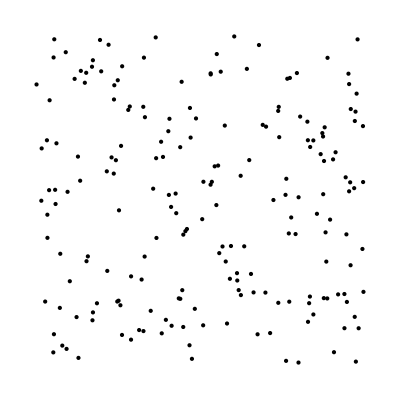

```mathematica
Graphics[Map[Point[#]&,bg[2][200]]]
```

```mathematica
(*Export["bg-2-200.tsv",bg[2][200]]*)
```

```mathematica
(*Export["bg-2-400.tsv",bg[2][400]]*)
```

```mathematica
(*Export["bg-2-600.tsv",bg[2][600]]*)
```

```mathematica
(*Export["bg-2-800.tsv",bg[2][800]]*)
```

```mathematica
(*Export["bg-2-1000.tsv",bg[2][1000]]*)
```

## 2D, normaldist;single, 2 - 20; 2

```mathematica
nd[2][2]=Table[{RandomVariate[NormalDistribution[]],RandomVariate[NormalDistribution[]]},{2}];
```

```mathematica
For[i=2,i≤20,i+=2,Print[i];
nd[2][i]=Table[{RandomVariate[NormalDistribution[]],RandomVariate[NormalDistribution[]]},{i}];
]
```

2

4

6

8

10

12

14

16

18

20

## 2D, normaldist;single, 200 - 1600; 200

```mathematica
nd[2][200]=Table[{RandomVariate[NormalDistribution[]],RandomVariate[NormalDistribution[]]},{200}];
```

```mathematica
nd[2][400]=Table[{RandomVariate[NormalDistribution[]],RandomVariate[NormalDistribution[]]},{400}];
```

```mathematica
nd[2][400]=Table[{RandomVariate[NormalDistribution[]],RandomVariate[NormalDistribution[]]},{400}];
```

```mathematica
nd[2][600]=Table[{RandomVariate[NormalDistribution[]],RandomVariate[NormalDistribution[]]},{600}];
```

```mathematica
nd[2][800]=Table[{RandomVariate[NormalDistribution[]],RandomVariate[NormalDistribution[]]},{800}];
```

```mathematica
nd[2][1000]=Table[{RandomVariate[NormalDistribution[]],RandomVariate[NormalDistribution[]]},{1000}];
```

```mathematica
nd[2][1200]=Table[{RandomVariate[NormalDistribution[]],RandomVariate[NormalDistribution[]]},{1200}];
```

```mathematica
nd[2][1400]=Table[{RandomVariate[NormalDistribution[]],RandomVariate[NormalDistribution[]]},{1400}];
```

```mathematica
nd[2][1600]=Table[{RandomVariate[NormalDistribution[]],RandomVariate[NormalDistribution[]]},{1600}];
```

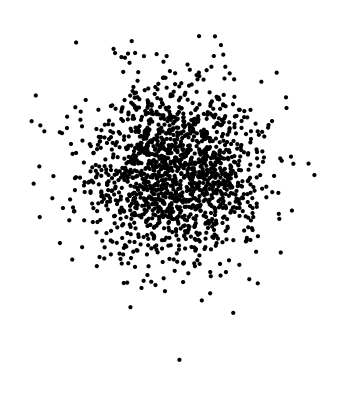

```mathematica
Graphics[Map[Point[#]&,nd[2][1600]]]
```

## 2D, 3Cls

```mathematica
correctdata[2][2][3]={Map[#+{0,0}&,nd[2][2]],Map[#+{5,0}&,nd[2][2]],Map[#+{2.5,3.5}&,nd[2][2]]}
```

{{{-1.07292,1.05281},{1.16178,-0.0713975}},{{3.92708,1.05281},{6.16178,-0.0713975}},{{1.42708,4.55281},{3.66178,3.4286}}}

```mathematica
makeRClusterFromMMAClData[correctdata[2][2][3]]
```

{{-1.07292,1.05281,1},{1.16178,-0.0713975,1},{3.92708,1.05281,2},{6.16178,-0.0713975,2},{1.42708,4.55281,3},{3.66178,3.4286,3}}

```mathematica
Directory[]
```

/Users/amanokou/gitsrc/ClusteringAdequation/data

```mathematica
(*Export["correctdata_2_2_3.tsv",correctdata[2][2][3]//makeRClusterFromMMAClData]*)
```

```mathematica
correctdata[2][4][3]={Map[#+{0,0}&,nd[2][4]],Map[#+{5,0}&,nd[2][4]],Map[#+{2.5,3.5}&,nd[2][4]]}
```

{{{0.230157,-1.1394},{0.770119,-0.255787},{0.448683,1.44828},{0.271494,1.35189}},{{5.23016,-1.1394},{5.77012,-0.255787},{5.44868,1.44828},{5.27149,1.35189}},{{2.73016,2.3606},{3.27012,3.24421},{2.94868,4.94828},{2.77149,4.85189}}}

```mathematica
(*Export["correctdata_2_4_3.tsv",correctdata[2][4][3]//makeRClusterFromMMAClData]*)
```

```mathematica
correctdata[2][6][3]={Map[#+{0,0}&,nd[2][6]],Map[#+{5,0}&,nd[2][6]],Map[#+{2.5,3.5}&,nd[2][6]]}
```

{{{1.67529,-0.757693},{-0.0326276,-1.84869},{0.573159,2.89139},{1.17294,1.39343},{0.434931,0.42402},{-1.01571,1.81504}},{{6.67529,-0.757693},{4.96737,-1.84869},{5.57316,2.89139},{6.17294,1.39343},{5.43493,0.42402},{3.98429,1.81504}},{{4.17529,2.74231},{2.46737,1.65131},{3.07316,6.39139},{3.67294,4.89343},{2.93493,3.92402},{1.48429,5.31504}}}

```mathematica
(*Export["correctdata_2_6_3.tsv",correctdata[2][6][3]//makeRClusterFromMMAClData]*)
```

## 2D, orverlapped

```mathematica
ndOv[2,1]=Join[Map[#+{1,3.6}&,nd[2][400]],Map[#&,nd[2][400]],Map[#+{10,2}&,nd[2][400]]];
```

```mathematica
Dimensions[ndOv[2,1]]
```

{1200,2}

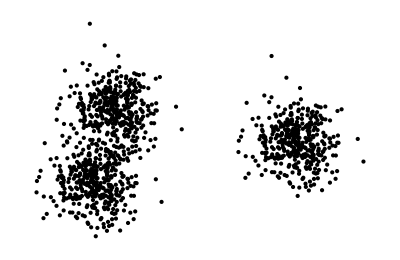

```mathematica
Graphics[Map[Point[#]&,ndOv[2,1]]]
```

```mathematica
(*Export["overlapped2D.tsv",ndOv[2,1]]*)
```

## 2D, unbalanced

```mathematica
ndUb[3]=Join[Map[#+{1,6}&,nd[2][400]],Map[#*0.5&,nd[2][400]],Map[#+{10,2}&,nd[2][400]]];
```

```mathematica
Dimensions[ndUb[3]]
```

{1200,2}

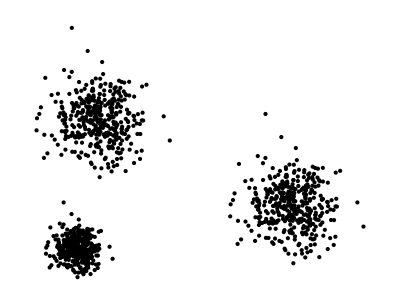

```mathematica
Graphics[Map[Point[#]&,ndUb[3]]]
```

```mathematica
(*Export["unbalanced2D.tsv",ndUb[3]]*)
```

```mathematica
(*Export["unbalanced2D_x10.tsv",ndUb[3]*10]*)
```

```mathematica
(*Export["unbalanced2D_x10E-1.tsv",ndUb[3]/10]*)
```

## 2D, subcluster

```mathematica
ndSubs[5]=Join[Map[#+{0,0}&,nd[2][400]],Map[#*1.1+{0,6}&,nd[2][400]],Map[#*1.2+{18,0}&,nd[2][400]],Map[#+{17,6}&,nd[2][400]],Map[#*1.4+{7,17}&,nd[2][400]]];
```

```mathematica
Dimensions[ndSubs[5]]
```

{2000,2}

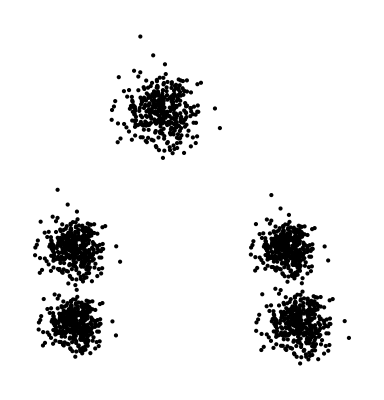

```mathematica
Graphics[Map[Point[#]&,ndSubs[5]]]
```

```mathematica
(*Export["subcluster2D.tsv",ndSubs[5]]*)
```

## 2D, noisy

```mathematica
shifts={{6.8,2.5},{4.5,6.1},{4.0,3.2},{2.0,1.7},{8.5,4.8},{2.0,5.4},{5.9,0.3}}
```

{{6.8,2.5},{4.5,6.1},{4.,3.2},{2.,1.7},{8.5,4.8},{2.,5.4},{5.9,0.3}}

```mathematica
scales={0.25,0.3,0.18,0.3,0.28,0.3,0.3}
```

{0.25,0.3,0.18,0.3,0.28,0.3,0.3}

```mathematica
(nd[7,"correct"]=Table[Map[#*scales[[n]]+shifts[[n]]&,nd[2][200]],{n,Length[shifts]}])//Length
```

7

```mathematica
nd[7,"correct","centroids"]=Map[Mean[#]&,nd[7,"correct"]]
```

{{6.77949,2.48471},{4.47539,6.08165},{3.98523,3.18899},{1.97539,1.68165},{8.47703,4.78288},{1.97539,5.38165},{5.87539,0.281652}}

```mathematica
nd[7,"correct","1/10","centroids"]=Map[Mean[#]&,nd[7,"correct"]/10]
```

{{0.677949,0.248471},{0.447539,0.608165},{0.398523,0.318899},{0.197539,0.168165},{0.847703,0.478288},{0.197539,0.538165},{0.587539,0.0281652}}

```mathematica
(nd[7]=Flatten[Table[Map[#*scales[[n]]+shifts[[n]]&,nd[2][200]],{n,Length[shifts]}],1])//Dimensions
```

{1400,2}

```mathematica
(nd[7,"correct","R"]=createClusterdFileR[nd[7,"correct"]])//Length
```

1400

```mathematica
(nd[7,"correct","R","1/10"]=createClusterdFileR[nd[7,"correct"]/10])//Length
```

1400

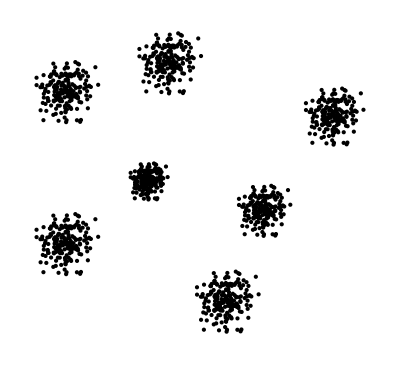

```mathematica
Graphics[Map[Point[#]&,nd[7]],PlotRange->All]
```

```mathematica
(*Export["nd7.tsv",nd[7]]*)
```

```mathematica
(*Export["nd7_x10E-1.tsv",nd[7]/10]*)
```

```mathematica
nd[7,"correct","R"]//Length
```

1400

```mathematica
(*Export["nd7_correct_R.tsv",nd[7,"correct","R"]]*)
```

```mathematica
(*Export["nd7_correct_R.cent.tsv",nd[7,"correct","centroids"]]*)
```

```mathematica
(*Export["nd7_correct_R_x10E-1.tsv",nd[7,"correct","R","1/10"]]*)
```

```mathematica
(*Export["nd7_correct_R_x10E-1.cent.tsv",nd[7,"correct","1/10","centroids"]]*)
```

```mathematica
FindClusters[nd[7],Method->"Agglomerate"]//Length
```

1

```mathematica
nois=Map[#+{5,3.2}&,bg[2][400]*5.4];
```

```mathematica
noisy[7]=Join[nd[7],nois];
```

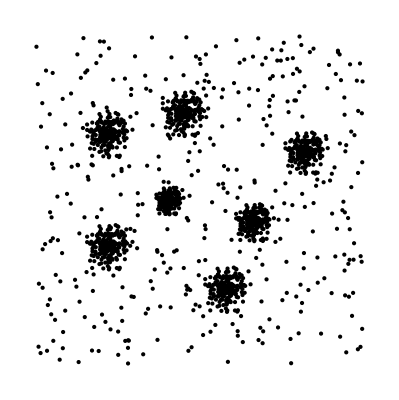

```mathematica
Graphics[Map[Point[#]&,noisy[7]]]
```

```mathematica
(*Export["noisy7.tsv",noisy[7]]*)
```

```mathematica
(*Export["noisy7_x10E-1.tsv",noisy[7]/10]*)
```

```mathematica
FindClusters[noisy[7],7,Method->"Optimize"]//Length
```

7

```mathematica
FindClusters[noisy[7],Method->"Agglomerate"]//Length
```

1

```mathematica
FindClusters[noisy[7],Method->"Optimize"]//Length
```

2

## 2D, 60 samples, 6 clusters, each cluster has 10 samples.

わかりやすいデータ、6クラスタ、60サンプル、各クラスタに10メンバー、2次元

```mathematica
rt6=Map[polarToxy[{1,#}]&,Table[2 Pi n/6,{n,1,6}]]
```

{{1/2,(√3)/2},{-1/2,(√3)/2},{-1,0},{-1/2,-(√3)/2},{1/2,-(√3)/2},{1,0}}

```mathematica
Graphics[Map[Point[#]&,rt6]]
```

-Graphics-

```mathematica
dataCLrt6=Transpose[Table[rt6,{10}]]
```

{{{1/2,(√3)/2},{1/2,(√3)/2},{1/2,(√3)/2},{1/2,(√3)/2},{1/2,(√3)/2},{1/2,(√3)/2},{1/2,(√3)/2},{1/2,(√3)/2},{1/2,(√3)/2},{1/2,(√3)/2}},{{-1/2,(√3)/2},{-1/2,(√3)/2},{-1/2,(√3)/2},{-1/2,(√3)/2},{-1/2,(√3)/2},{-1/2,(√3)/2},{-1/2,(√3)/2},{-1/2,(√3)/2},{-1/2,(√3)/2},{-1/2,(√3)/2}},{{-1,0},{-1,0},{-1,0},{-1,0},{-1,0},{-1,0},{-1,0},{-1,0},{-1,0},{-1,0}},{{-1/2,-(√3)/2},{-1/2,-(√3)/2},{-1/2,-(√3)/2},{-1/2,-(√3)/2},{-1/2,-(√3)/2},{-1/2,-(√3)/2},{-1/2,-(√3)/2},{-1/2,-(√3)/2},{-1/2,-(√3)/2},{-1/2,-(√3)/2}},{{1/2,-(√3)/2},{1/2,-(√3)/2},{1/2,-(√3)/2},{1/2,-(√3)/2},{1/2,-(√3)/2},{1/2,-(√3)/2},{1/2,-(√3)/2},{1/2,-(√3)/2},{1/2,-(√3)/2},{1/2,-(√3)/2}},{{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0}}}

```mathematica
dataFLrt6=Flatten[dataCLrt6,1]
```

{{1/2,(√3)/2},{1/2,(√3)/2},{1/2,(√3)/2},{1/2,(√3)/2},{1/2,(√3)/2},{1/2,(√3)/2},{1/2,(√3)/2},{1/2,(√3)/2},{1/2,(√3)/2},{1/2,(√3)/2},{-1/2,(√3)/2},{-1/2,(√3)/2},{-1/2,(√3)/2},{-1/2,(√3)/2},{-1/2,(√3)/2},{-1/2,(√3)/2},{-1/2,(√3)/2},{-1/2,(√3)/2},{-1/2,(√3)/2},{-1/2,(√3)/2},{-1,0},{-1,0},{-1,0},{-1,0},{-1,0},{-1,0},{-1,0},{-1,0},{-1,0},{-1,0},{-1/2,-(√3)/2},{-1/2,-(√3)/2},{-1/2,-(√3)/2},{-1/2,-(√3)/2},{-1/2,-(√3)/2},{-1/2,-(√3)/2},{-1/2,-(√3)/2},{-1/2,-(√3)/2},{-1/2,-(√3)/2},{-1/2,-(√3)/2},{1/2,-(√3)/2},{1/2,-(√3)/2},{1/2,-(√3)/2},{1/2,-(√3)/2},{1/2,-(√3)/2},{1/2,-(√3)/2},{1/2,-(√3)/2},{1/2,-(√3)/2},{1/2,-(√3)/2},{1/2,-(√3)/2},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0}}

```mathematica
(*Export["dataFLrt6.tsv",dataFLrt6]*)
```

## 2D, 50 samples, 10 clusters

```mathematica
rt10=Map[polarToxy[{1,#}]&,Table[2 Pi n/10,{n,1,10}]]//N
```

{{0.809017,0.587785},{0.309017,0.951057},{-0.309017,0.951057},{-0.809017,0.587785},{-1.,0.},{-0.809017,-0.587785},{-0.309017,-0.951057},{0.309017,-0.951057},{0.809017,-0.587785},{1.,0.}}

```mathematica
rt10table5=Transpose[Table[rt10,{5}]];
```

```mathematica
rt10table5R=makeRClusterFromMMAClData[rt10table5]
```

{{0.809017,0.587785,1},{0.809017,0.587785,1},{0.809017,0.587785,1},{0.809017,0.587785,1},{0.809017,0.587785,1},{0.309017,0.951057,2},{0.309017,0.951057,2},{0.309017,0.951057,2},{0.309017,0.951057,2},{0.309017,0.951057,2},{-0.309017,0.951057,3},{-0.309017,0.951057,3},{-0.309017,0.951057,3},{-0.309017,0.951057,3},{-0.309017,0.951057,3},{-0.809017,0.587785,4},{-0.809017,0.587785,4},{-0.809017,0.587785,4},{-0.809017,0.587785,4},{-0.809017,0.587785,4},{-1.,0.,5},{-1.,0.,5},{-1.,0.,5},{-1.,0.,5},{-1.,0.,5},{-0.809017,-0.587785,6},{-0.809017,-0.587785,6},{-0.809017,-0.587785,6},{-0.809017,-0.587785,6},{-0.809017,-0.587785,6},{-0.309017,-0.951057,7},{-0.309017,-0.951057,7},{-0.309017,-0.951057,7},{-0.309017,-0.951057,7},{-0.309017,-0.951057,7},{0.309017,-0.951057,8},{0.309017,-0.951057,8},{0.309017,-0.951057,8},{0.309017,-0.951057,8},{0.309017,-0.951057,8},{0.809017,-0.587785,9},{0.809017,-0.587785,9},{0.809017,-0.587785,9},{0.809017,-0.587785,9},{0.809017,-0.587785,9},{1.,0.,10},{1.,0.,10},{1.,0.,10},{1.,0.,10},{1.,0.,10}}

```mathematica
(*Export["rt10table5R.tsv",rt10table5R]*)
```

```mathematica
Directory[]
```

/Users/amanokou/gitsrc/ClusteringAdequation/data

## 2D, 100 samples, 10 clusters

```mathematica
rt10=Map[polarToxy[{1,#}]&,Table[2 Pi n/10,{n,1,10}]]//N
```

{{0.809017,0.587785},{0.309017,0.951057},{-0.309017,0.951057},{-0.809017,0.587785},{-1.,0.},{-0.809017,-0.587785},{-0.309017,-0.951057},{0.309017,-0.951057},{0.809017,-0.587785},{1.,0.}}

```mathematica
rt10table10=Transpose[Table[rt10,{10}]];
```

```mathematica
rt10table10R=makeRClusterFromMMAClData[rt10table10]
```

{{0.809017,0.587785,1},{0.809017,0.587785,1},{0.809017,0.587785,1},{0.809017,0.587785,1},{0.809017,0.587785,1},{0.809017,0.587785,1},{0.809017,0.587785,1},{0.809017,0.587785,1},{0.809017,0.587785,1},{0.809017,0.587785,1},{0.309017,0.951057,2},{0.309017,0.951057,2},{0.309017,0.951057,2},{0.309017,0.951057,2},{0.309017,0.951057,2},{0.309017,0.951057,2},{0.309017,0.951057,2},{0.309017,0.951057,2},{0.309017,0.951057,2},{0.309017,0.951057,2},{-0.309017,0.951057,3},{-0.309017,0.951057,3},{-0.309017,0.951057,3},{-0.309017,0.951057,3},{-0.309017,0.951057,3},{-0.309017,0.951057,3},{-0.309017,0.951057,3},{-0.309017,0.951057,3},{-0.309017,0.951057,3},{-0.309017,0.951057,3},{-0.809017,0.587785,4},{-0.809017,0.587785,4},{-0.809017,0.587785,4},{-0.809017,0.587785,4},{-0.809017,0.587785,4},{-0.809017,0.587785,4},{-0.809017,0.587785,4},{-0.809017,0.587785,4},{-0.809017,0.587785,4},{-0.809017,0.587785,4},{-1.,0.,5},{-1.,0.,5},{-1.,0.,5},{-1.,0.,5},{-1.,0.,5},{-1.,0.,5},{-1.,0.,5},{-1.,0.,5},{-1.,0.,5},{-1.,0.,5},{-0.809017,-0.587785,6},{-0.809017,-0.587785,6},{-0.809017,-0.587785,6},{-0.809017,-0.587785,6},{-0.809017,-0.587785,6},{-0.809017,-0.587785,6},{-0.809017,-0.587785,6},{-0.809017,-0.587785,6},{-0.809017,-0.587785,6},{-0.809017,-0.587785,6},{-0.309017,-0.951057,7},{-0.309017,-0.951057,7},{-0.309017,-0.951057,7},{-0.309017,-0.951057,7},{-0.309017,-0.951057,7},{-0.309017,-0.951057,7},{-0.309017,-0.951057,7},{-0.309017,-0.951057,7},{-0.309017,-0.951057,7},{-0.309017,-0.951057,7},{0.309017,-0.951057,8},{0.309017,-0.951057,8},{0.309017,-0.951057,8},{0.309017,-0.951057,8},{0.309017,-0.951057,8},{0.309017,-0.951057,8},{0.309017,-0.951057,8},{0.309017,-0.951057,8},{0.309017,-0.951057,8},{0.309017,-0.951057,8},{0.809017,-0.587785,9},{0.809017,-0.587785,9},{0.809017,-0.587785,9},{0.809017,-0.587785,9},{0.809017,-0.587785,9},{0.809017,-0.587785,9},{0.809017,-0.587785,9},{0.809017,-0.587785,9},{0.809017,-0.587785,9},{0.809017,-0.587785,9},{1.,0.,10},{1.,0.,10},{1.,0.,10},{1.,0.,10},{1.,0.,10},{1.,0.,10},{1.,0.,10},{1.,0.,10},{1.,0.,10},{1.,0.,10}}

```mathematica
(*Export["rt10table10R.tsv",rt10table10R]*)
```

```mathematica
Directory[]
```

/Users/amanokou/gitsrc/ClusteringAdequation/data

## 10D, 100 samples, 10 clusters

```mathematica
id10=IdentityMatrix[10];
```

```mathematica
id10Table10=Transpose[Table[id10,{10}]];
```

```mathematica
id10Table10R=makeRClusterFromMMAClData[id10Table10]
```

{{1,0,0,0,0,0,0,0,0,0,1},{1,0,0,0,0,0,0,0,0,0,1},{1,0,0,0,0,0,0,0,0,0,1},{1,0,0,0,0,0,0,0,0,0,1},{1,0,0,0,0,0,0,0,0,0,1},{1,0,0,0,0,0,0,0,0,0,1},{1,0,0,0,0,0,0,0,0,0,1},{1,0,0,0,0,0,0,0,0,0,1},{1,0,0,0,0,0,0,0,0,0,1},{1,0,0,0,0,0,0,0,0,0,1},{0,1,0,0,0,0,0,0,0,0,2},{0,1,0,0,0,0,0,0,0,0,2},{0,1,0,0,0,0,0,0,0,0,2},{0,1,0,0,0,0,0,0,0,0,2},{0,1,0,0,0,0,0,0,0,0,2},{0,1,0,0,0,0,0,0,0,0,2},{0,1,0,0,0,0,0,0,0,0,2},{0,1,0,0,0,0,0,0,0,0,2},{0,1,0,0,0,0,0,0,0,0,2},{0,1,0,0,0,0,0,0,0,0,2},{0,0,1,0,0,0,0,0,0,0,3},{0,0,1,0,0,0,0,0,0,0,3},{0,0,1,0,0,0,0,0,0,0,3},{0,0,1,0,0,0,0,0,0,0,3},{0,0,1,0,0,0,0,0,0,0,3},{0,0,1,0,0,0,0,0,0,0,3},{0,0,1,0,0,0,0,0,0,0,3},{0,0,1,0,0,0,0,0,0,0,3},{0,0,1,0,0,0,0,0,0,0,3},{0,0,1,0,0,0,0,0,0,0,3},{0,0,0,1,0,0,0,0,0,0,4},{0,0,0,1,0,0,0,0,0,0,4},{0,0,0,1,0,0,0,0,0,0,4},{0,0,0,1,0,0,0,0,0,0,4},{0,0,0,1,0,0,0,0,0,0,4},{0,0,0,1,0,0,0,0,0,0,4},{0,0,0,1,0,0,0,0,0,0,4},{0,0,0,1,0,0,0,0,0,0,4},{0,0,0,1,0,0,0,0,0,0,4},{0,0,0,1,0,0,0,0,0,0,4},{0,0,0,0,1,0,0,0,0,0,5},{0,0,0,0,1,0,0,0,0,0,5},{0,0,0,0,1,0,0,0,0,0,5},{0,0,0,0,1,0,0,0,0,0,5},{0,0,0,0,1,0,0,0,0,0,5},{0,0,0,0,1,0,0,0,0,0,5},{0,0,0,0,1,0,0,0,0,0,5},{0,0,0,0,1,0,0,0,0,0,5},{0,0,0,0,1,0,0,0,0,0,5},{0,0,0,0,1,0,0,0,0,0,5},{0,0,0,0,0,1,0,0,0,0,6},{0,0,0,0,0,1,0,0,0,0,6},{0,0,0,0,0,1,0,0,0,0,6},{0,0,0,0,0,1,0,0,0,0,6},{0,0,0,0,0,1,0,0,0,0,6},{0,0,0,0,0,1,0,0,0,0,6},{0,0,0,0,0,1,0,0,0,0,6},{0,0,0,0,0,1,0,0,0,0,6},{0,0,0,0,0,1,0,0,0,0,6},{0,0,0,0,0,1,0,0,0,0,6},{0,0,0,0,0,0,1,0,0,0,7},{0,0,0,0,0,0,1,0,0,0,7},{0,0,0,0,0,0,1,0,0,0,7},{0,0,0,0,0,0,1,0,0,0,7},{0,0,0,0,0,0,1,0,0,0,7},{0,0,0,0,0,0,1,0,0,0,7},{0,0,0,0,0,0,1,0,0,0,7},{0,0,0,0,0,0,1,0,0,0,7},{0,0,0,0,0,0,1,0,0,0,7},{0,0,0,0,0,0,1,0,0,0,7},{0,0,0,0,0,0,0,1,0,0,8},{0,0,0,0,0,0,0,1,0,0,8},{0,0,0,0,0,0,0,1,0,0,8},{0,0,0,0,0,0,0,1,0,0,8},{0,0,0,0,0,0,0,1,0,0,8},{0,0,0,0,0,0,0,1,0,0,8},{0,0,0,0,0,0,0,1,0,0,8},{0,0,0,0,0,0,0,1,0,0,8},{0,0,0,0,0,0,0,1,0,0,8},{0,0,0,0,0,0,0,1,0,0,8},{0,0,0,0,0,0,0,0,1,0,9},{0,0,0,0,0,0,0,0,1,0,9},{0,0,0,0,0,0,0,0,1,0,9},{0,0,0,0,0,0,0,0,1,0,9},{0,0,0,0,0,0,0,0,1,0,9},{0,0,0,0,0,0,0,0,1,0,9},{0,0,0,0,0,0,0,0,1,0,9},{0,0,0,0,0,0,0,0,1,0,9},{0,0,0,0,0,0,0,0,1,0,9},{0,0,0,0,0,0,0,0,1,0,9},{0,0,0,0,0,0,0,0,0,1,10},{0,0,0,0,0,0,0,0,0,1,10},{0,0,0,0,0,0,0,0,0,1,10},{0,0,0,0,0,0,0,0,0,1,10},{0,0,0,0,0,0,0,0,0,1,10},{0,0,0,0,0,0,0,0,0,1,10},{0,0,0,0,0,0,0,0,0,1,10},{0,0,0,0,0,0,0,0,0,1,10},{0,0,0,0,0,0,0,0,0,1,10},{0,0,0,0,0,0,0,0,0,1,10}}

## 10D, 50 samples, 10 clusters

```mathematica
id10=IdentityMatrix[10];
```

```mathematica
id10Table5=Transpose[Table[id10,{5}]];
```

```mathematica
id10Table5R=makeRClusterFromMMAClData[id10Table5]
```

{{1,0,0,0,0,0,0,0,0,0,1},{1,0,0,0,0,0,0,0,0,0,1},{1,0,0,0,0,0,0,0,0,0,1},{1,0,0,0,0,0,0,0,0,0,1},{1,0,0,0,0,0,0,0,0,0,1},{0,1,0,0,0,0,0,0,0,0,2},{0,1,0,0,0,0,0,0,0,0,2},{0,1,0,0,0,0,0,0,0,0,2},{0,1,0,0,0,0,0,0,0,0,2},{0,1,0,0,0,0,0,0,0,0,2},{0,0,1,0,0,0,0,0,0,0,3},{0,0,1,0,0,0,0,0,0,0,3},{0,0,1,0,0,0,0,0,0,0,3},{0,0,1,0,0,0,0,0,0,0,3},{0,0,1,0,0,0,0,0,0,0,3},{0,0,0,1,0,0,0,0,0,0,4},{0,0,0,1,0,0,0,0,0,0,4},{0,0,0,1,0,0,0,0,0,0,4},{0,0,0,1,0,0,0,0,0,0,4},{0,0,0,1,0,0,0,0,0,0,4},{0,0,0,0,1,0,0,0,0,0,5},{0,0,0,0,1,0,0,0,0,0,5},{0,0,0,0,1,0,0,0,0,0,5},{0,0,0,0,1,0,0,0,0,0,5},{0,0,0,0,1,0,0,0,0,0,5},{0,0,0,0,0,1,0,0,0,0,6},{0,0,0,0,0,1,0,0,0,0,6},{0,0,0,0,0,1,0,0,0,0,6},{0,0,0,0,0,1,0,0,0,0,6},{0,0,0,0,0,1,0,0,0,0,6},{0,0,0,0,0,0,1,0,0,0,7},{0,0,0,0,0,0,1,0,0,0,7},{0,0,0,0,0,0,1,0,0,0,7},{0,0,0,0,0,0,1,0,0,0,7},{0,0,0,0,0,0,1,0,0,0,7},{0,0,0,0,0,0,0,1,0,0,8},{0,0,0,0,0,0,0,1,0,0,8},{0,0,0,0,0,0,0,1,0,0,8},{0,0,0,0,0,0,0,1,0,0,8},{0,0,0,0,0,0,0,1,0,0,8},{0,0,0,0,0,0,0,0,1,0,9},{0,0,0,0,0,0,0,0,1,0,9},{0,0,0,0,0,0,0,0,1,0,9},{0,0,0,0,0,0,0,0,1,0,9},{0,0,0,0,0,0,0,0,1,0,9},{0,0,0,0,0,0,0,0,0,1,10},{0,0,0,0,0,0,0,0,0,1,10},{0,0,0,0,0,0,0,0,0,1,10},{0,0,0,0,0,0,0,0,0,1,10},{0,0,0,0,0,0,0,0,0,1,10}}

## 2D, 900 samples, 9 clusters

```mathematica
shiftClass={{0,0},{3,5},{-2,5},{12,12},{16.5,12},{14,17},{-9,18},{-5.3,21.5},{-5,16}}
```

{{0,0},{3,5},{-2,5},{12,12},{16.5,12},{14,17},{-9,18},{-5.3,21.5},{-5,16}}

```mathematica
createRandom2DND[n_]:=Table[{RandomVariate[NormalDistribution[]],RandomVariate[NormalDistribution[]]},{n}]
```

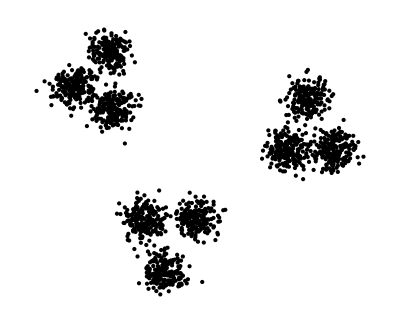

```mathematica
Graphics[Map[Point[#]&,random2D=Table[Map[shiftClass[[n]]+#&,createRandom2DND[200]],{n,Length[shiftClass]}],{2}]]
```

```mathematica
random2D
```

{{{0.172159,0.789904},{-0.6888,-0.466666},{-1.2882,0.330362},{1.27606,2.24522},{-0.347589,-0.95656},{-0.851251,0.341993},{1.21611,-0.579363},{-0.604922,-0.207657},{-1.06374,-0.97067},{0.665867,-0.0649522},{1.19496,0.253785},{0.151536,-0.197184},{-0.24784,0.212826},{-0.322593,0.0105064},{-2.05941,0.309514},{0.931049,-1.01936},{1.70516,0.661064},{1.23321,0.418346},{-0.635717,-0.215286},{0.298443,1.5857},{0.772234,-0.704964},{1.14961,1.839},{-1.17663,0.415929},{-0.163089,0.932032},{0.283988,0.342157},{-1.90781,-0.755696},{-0.295165,0.0803906},{-1.78442,0.491895},{0.195266,0.516835},{-0.181629,-1.12468},{-2.0381,0.809503},{-0.0689078,0.625102},{-1.95507,0.607553},{-0.420027,1.1486},{2.58035,1.11442},{1.13157,1.23161},{-0.27636,0.401129},{-2.04461,0.213692},{-0.0683429,-1.85371},{0.444147,-1.18806},{2.23007,1.60738},{-0.709328,1.82281},{0.997861,1.79357},{0.750978,-0.683469},{-0.352049,2.15729},{-1.08546,0.523626},{0.901748,-0.0915845},{-0.630084,-0.302186},{1.08289,-1.35678},{-0.124095,-1.02825},{1.29207,-0.322397},{1.42722,-1.01502},{1.36111,0.682339},{1.57459,-1.13272},{-0.483629,1.03995},{-0.30726,1.05031},{1.89322,0.635414},{1.30056,-0.36359},{0.957639,-0.314744},{0.505032,0.0724354},{1.09848,-0.377582},{1.21076,-1.06921},{0.730515,-2.55466},{0.700588,-0.502991},{-1.09086,-1.18621},{-0.287658,-0.632282},{0.402906,0.653914},{-0.104505,2.15843},{-0.51172,0.550222},{-0.836908,-1.3498},{1.42187,-0.183762},{-1.1318,1.51814},{0.746681,-1.15038},{-0.720114,0.0977486},{0.818491,1.01762},{0.543503,-1.67379},{-0.895695,0.209629},{0.172861,0.0403126},{2.08916,0.275889},{0.555557,-0.0966091},{0.543916,-0.366241},{1.35663,0.610164},{0.373949,1.38443},{-0.59324,0.913854},{-0.985138,-2.90572},{-1.23926,0.56858},{-0.479189,0.295175},{0.811737,1.42908},{0.769652,0.36247},{-1.12262,-0.18227},{-1.53616,-1.3139},{2.11119,1.50381},{1.20649,1.27093},{2.04276,0.333544},{0.358483,1.89783},{0.461104,-0.645038},{0.100714,0.326656},{-0.222273,1.41755},{2.25444,1.4924},{-0.196862,-0.625888}},{{3.94788,5.70718},{4.4993,5.51374},{4.96381,4.65651},{4.30861,4.55507},{2.10631,5.51938},{3.79758,5.28768},{3.45855,6.22348},{3.69555,2.61639},{5.94429,4.91985},{3.25803,6.30984},{6.44159,5.68694},{4.28059,5.85979},{4.88406,5.79266},{2.97145,6.19564},{2.8314,5.70777},{4.03745,5.08925},{4.98206,4.71934},{4.18191,4.24536},{3.48296,3.53599},{4.19125,4.86835},{5.52394,3.91654},{4.73321,4.9676},{3.84307,7.05781},{5.37655,3.19798},{4.95489,6.95868},{3.16813,3.75222},{4.36998,3.8323},{2.1879,3.63602},{2.48308,6.27041},{3.78842,5.0702},{2.72294,4.21406},{4.39683,5.45988},{3.63351,3.85906},{6.27555,1.91041},{3.07842,4.9856},{5.21788,2.96542},{4.46858,5.0607},{4.50068,4.69336},{4.16666,5.94858},{3.41776,6.23754},{4.45249,5.41328},{4.5906,3.75363},{2.98722,4.90045},{6.2575,4.70256},{4.13203,4.59447},{1.00145,4.99506},{3.22747,5.43184},{2.83812,5.82307},{4.78827,4.98244},{3.92014,5.89902},{3.57935,6.36243},{3.70625,5.40652},{2.10353,3.58843},{6.1913,4.24895},{3.15834,4.3321},{4.47894,4.47441},{3.1669,4.98945},{3.65924,6.24646},{5.71264,6.80519},{5.21433,4.74577},{3.59547,5.70606},{6.60417,4.25558},{4.02501,2.47249},{4.42554,7.40767},{4.50051,4.30991},{2.69696,3.39357},{4.10936,4.77467},{4.39583,4.55581},{5.94806,5.45604},{4.08977,6.53833},{5.51971,5.4265},{3.9924,4.87517},{3.76891,4.51318},{5.4613,4.44634},{2.38644,5.63218},{4.64513,5.67052},{4.38918,5.39552},{2.84999,5.49118},{3.41663,4.91298},{4.54536,6.01955},{5.21499,5.18191},{5.37062,4.169},{4.9926,4.56608},{6.05084,4.05698},{4.193,4.39437},{3.79678,8.17487},{3.07192,5.31988},{3.54869,4.21801},{4.54919,6.41862},{3.83511,6.07479},{4.77341,5.7927},{3.69288,5.04279},{3.75078,3.63989},{4.22724,5.9547},{5.16804,4.41133},{2.94535,4.95227},{6.23803,3.36311},{2.33782,2.56748},{3.97942,4.61685},{5.84079,5.57996}},{{-6.22155,8.30339},{-6.83906,5.60286},{-4.50362,7.57669},{-5.55072,5.9558},{-5.35539,4.8152},{-4.31696,6.80087},{-4.48482,5.97403},{-3.59117,6.32448},{-6.69197,5.83997},{-3.87349,3.75097},{-3.47405,6.78744},{-5.35994,4.86561},{-6.15364,6.58109},{-6.31162,6.6698},{-6.52542,5.66435},{-5.72396,7.86759},{-5.26836,6.85169},{-4.57434,5.24029},{-5.91241,6.56711},{-5.14677,7.21019},{-6.75645,5.3792},{-4.67492,7.32674},{-5.97448,4.95021},{-6.07639,4.96434},{-3.54606,6.59609},{-4.89605,5.12795},{-4.43979,7.13632},{-5.18907,6.47529},{-4.64254,5.84238},{-4.22911,5.06665},{-2.8826,7.14239},{-5.27864,6.57413},{-6.34864,6.67596},{-6.6206,5.70105},{-4.76934,4.49259},{-5.79486,5.03778},{-5.0586,5.3648},{-5.10467,5.58904},{-5.53464,6.87319},{-4.92836,5.7721},{-5.88555,4.90564},{-6.62819,4.72246},{-6.67383,4.39574},{-4.78197,6.12409},{-5.9745,5.2844},{-4.92866,7.24915},{-3.30395,5.0579},{-3.75663,6.52385},{-3.94597,6.34053},{-4.13194,5.37015},{-5.09927,7.04863},{-5.43323,6.08312},{-5.03427,6.39889},{-6.44601,6.19929},{-4.62813,4.16899},{-3.34708,5.45523},{-5.32194,6.74985},{-5.84359,5.64541},{-2.62888,8.00024},{-4.53267,5.79294},{-5.14775,6.19717},{-2.90224,4.82819},{-5.26631,4.72585},{-3.24374,6.59283},{-5.43048,7.16233},{-5.6402,4.25267},{-6.2893,7.23218},{-4.74542,4.75395},{-6.28692,5.86796},{-4.24683,6.64528},{-5.14994,4.88547},{-4.03751,5.30193},{-5.28548,7.29064},{-5.01338,6.00172},{-5.2165,6.07839},{-4.63646,7.2363},{-6.31759,4.60907},{-5.48707,7.243},{-3.74495,8.05255},{-5.76156,4.86859},{-5.1872,6.93362},{-5.08005,6.31978},{-5.10927,8.11815},{-5.19191,7.41644},{-4.0876,5.54711},{-5.13414,7.05661},{-4.95172,5.18628},{-5.80425,5.28683},{-5.11183,6.73888},{-4.18102,6.46927},{-5.77269,5.91269},{-5.64769,6.70802},{-5.83756,6.74988},{-5.47874,5.64172},{-5.31461,7.96644},{-3.22549,7.3542},{-3.60006,5.72183},{-6.77955,4.55558},{-3.8426,5.43257},{-6.76605,5.49215}}}

## TEST